## Initialization

```mathematica
myPrint[msg_,rest_]:=Print[StringForm@@Flatten[{msg,rest}]];
g=9.81;
l=1;(*Pool length*)
h=0.3;(*Pool depth*)
tMax=1;

(*Surface variable*)
hInitial[x_]:=1/((0.2)2π)Exp[-0.5((x/l-0.3)/0.05)^2];
hVal=NIntegrate[hInitial[x],{x,0,l}]/l;
hNorm[x_]:=hInitial[x]-hVal;

(*Matrix helper*)
centerIdx=1;
leftIdx=2;
rightIdx=3;
bottomIdx=4;
topIdx=5;
```

## Function definitions

```mathematica
calcStep[xIntervals_Integer,zIntervals_Integer,tIntervals_Integer]:=(
n=xIntervals+1;
m=zIntervals+1;
t=tIntervals+1;
numNodes=n*m;
Δx=N[l/xIntervals];
Δz=N[h/zIntervals];
τ=N[tMax/tIntervals];

xCoord=Table[Δx(i-1),{i,1,n}];
zCoord=Table[Δz(j-1)-h,{j,1,m}];
tCoord=Table[τ(t-1),{t,1,t}];
index=Table[1+(i-1)m+(j-1),{i,1,n},{j,1,m}];
);
buildMatrix[tIndex_Integer]:=Module[{i,j,result,center,left,right,bottom,top,mainIdx,tg},
(*Sparce matrix. We only need the center and 4 neighbors from each cell*)
result=Table[0.0,numNodes,5];

(*Add contributions to nodes below the free surface*)
For[j=1,j≤m-1,j++,
For[i=1,i≤n,i++,
center=-2.0(Δx/Δz)-2.0(Δz/Δx);
left=right=Δz/Δx;
top=bottom=Δx/Δz;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];
If[j==1,
(*Bottom boundary*)
top+=bottom;
bottom=0;
];

mainIdx=index[[i,j]];
result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;
];
];

(*Add contributions to nodes on the free surface*)
tg=τ^2 g;
For[i=1,i≤n,i++,
center=-(4+tg/Δz+(tg Δz)/Δx^2);
left=right=(tg Δz)/(2 Δx^2);
bottom=tg/Δz;
top=0;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];

mainIdx=index[[i,m]];
result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;
];

Return[result];
];
buildRightSide[tIndex_Integer,ϕ_,hi_]:=Module[{result,i,tg,mainIdx},
result=Table[0.0,numNodes];

(*Contributions from nodes on the free surface*)
tg=τ g;
For[i=1,i≤n,i++,
mainIdx=index[[i,m]];
result[[mainIdx]]=-4ϕ[[mainIdx]]+τ(4 g hi[[i]]
+tg/Δz(ϕ[[mainIdx]]-ϕ[[index[[i,m-1]]]])
+(tg Δz)/Δx^2 ϕ[[mainIdx]]
-(tg Δz)/(2 Δx^2)(ϕ[[index[[If[i>1,i-1,i+1],m]]]]+ϕ[[index[[If[i<n,i+1,i-1],m]]]])
);
];
Return[result];
];
(*Find the solution of X's of the given tridiagonal block matrix
@param matrix A table of n*m vectors of 5 elements. These are all the non-zero elements in the actual matrix.
@param rhx A vector of n*m elements. This is the right hand side of the linear system.
@param n The number of blocks.
@param m The size of each block. They are square.
The time complexity of the algorithm is O(n*m^3). For better performance pick n>m.
*)
solveBlockTridiag[matrix_,rhs_,n_,m_]:=Module[{w,f,k,i,a,b,result},
w=Table[0,n];
f=Table[0,n];
k=Table[0,n];
w[[1]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1;;m,centerIdx]],
Band[{2,1}]->matrix[[2;;m,bottomIdx]],
Band[{1,2}]->matrix[[1;;m-1,topIdx]]},{m,m}]];
f[[1]]=w[[1]].rhs[[1;;m]];
k[[1]]=w[[1]].SparseArray[Band[{1,1}]->matrix[[1;;m,rightIdx]],{m,m}];

For[i=2,i≤n-1,i++,
a=SparseArray[Band[{1,1}]->matrix[[1+(i-1)m;;i m,leftIdx]],{m,m}];
b=SparseArray[Band[{1,1}]->matrix[[1+(i-1)m;;i m,rightIdx]],{m,m}];
w[[i]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1+(i-1)m;;i m,centerIdx]],
Band[{2,1}]->matrix[[2+(i-1)m;;i m,bottomIdx]],
Band[{1,2}]->matrix[[1+(i-1)m;;i m-1,topIdx]]},{m,m}]
-a.k[[i-1]]];
f[[i]]=w[[i]].(rhs[[1+(i-1)m;;i m]]-a.f[[i-1]]);
k[[i]]=w[[i]].b;
];

result=Table[0,n m];
a=SparseArray[Band[{1,1}]->matrix[[1+(n-1) m;;n m,leftIdx]],{m,m}];
w[[n]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1+(n-1) m;;n m,centerIdx]],
Band[{2,1}]->matrix[[2+(n-1) m;;n m,bottomIdx]],
Band[{1,2}]->matrix[[1+(n-1) m;;n m-1,topIdx]]},{m,m}]
-a.k[[n-1]]];
result[[1+(n-1) m;;n m]]=w[[n]].(rhs[[1+(n-1) m;;n m]]-a.f[[n-1]]);
For[i=n-1,i≥1,i--,
result[[1+(i-1) m;;i m]]=f[[i]]-k[[i]].result[[1+i m;;(i+1) m]];
];

Return[result];
];
```

## Solve linear system using block tri-diagonal solver

Done!

Done!

Done!

«5 more identical outputs»

Max error convergence F = {0.742872,2.46676,1.87012,1.96699,1.99176,1.99794,1.99949}

Max error convergence H = {0.459832,1.10051,1.8217,2.00329,2.00531,2.00163,2.00043}

L2 norm convergence F = {1.46042,2.00679,2.05897,1.98856,1.99545,1.99877,1.99969}

L2 norm convergence H = {0.814459,1.27164,1.93213,2.02335,2.00908,2.00248,2.00064}

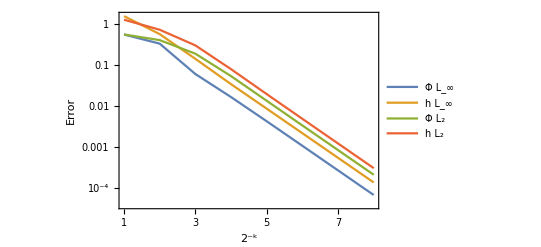

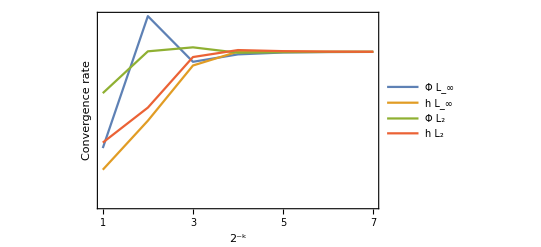

```mathematica
getSolutions[xIntervals_,zIntervals_,tIntervals_]:=
Module[{mat,rhs,i,j,k,ϕ,hi,kCurr,kPrev,elapseT,hRem,mRem,sRem,tTotal,tRem,solutionF,solutionH},Monitor[
calcStep[xIntervals,zIntervals,tIntervals];
solutionH=None;
solutionF=Table[0,t];

hi=Table[0.0,{i,1,t},{j,1,n}];
For[i=1,i≤n,i++,hi[[1,i]]=hNorm[xCoord[[i]]]];
ϕ=Table[0.0,2,numNodes];
solutionF[[1]]=ϕ[[1]];

tTotal=0;
hRem=99;
mRem=99;
sRem=99;
For[k=2,k≤t,k++,
kCurr=1+Mod[k,2];
kPrev=1+Mod[k-1,2];
elapseT=AbsoluteTiming[
mat=buildMatrix[k-1];
rhs=buildRightSide[k-1,ϕ[[kPrev]],hi[[k-1]]];
ϕ[[kCurr]]=solveBlockTridiag[mat,rhs,n,m];
solutionF[[k]]=ϕ[[kCurr]];

(*Update the free surface height*)
For[i=1,i≤n,i++,
hi[[k,i]]=-(2/(τ g)(ϕ[[kCurr,index[[i,m]]]]-ϕ[[kPrev,index[[i,m]]]])+hi[[k-1,i]]);
];
][[1]];
tTotal+=elapseT;
tRem=tTotal(t-1)/(k-1)-tTotal;
hRem=Floor[tRem/3600];
mRem=Floor[Mod[tRem,3600]/60];
sRem=Floor[Mod[tRem,60]];
];
myPrint["Done!",{}];
solutionH=hi;

,Row[{ProgressIndicator[(k-1)/(t-1)],StringForm["``/``, Time remaining: ``h, ``m, ``s",(k-1),(t-1),hRem,mRem,sRem]}," "]];
Return[{solutionF,solutionH}];
];

numLevels=8;
intervals={6,3,6};
solutionsF=Table[0,numLevels];
solutionsH=Table[0,numLevels];
Module[{l,stride,res,n,m},
For[l=1,l≤numLevels,l++,
stride=2^(l-1);
{n,m}=stride*intervals[[1;;2]]+1;
res=getSolutions@@(intervals*stride);

solutionsF[[l]]=res[[1]][[1;;All;;stride]];
solutionsF[[l]]=(ArrayReshape[#,{n,m}]&)/@solutionsF[[l]];
solutionsF[[l]]=(Flatten[#[[1;;All;;stride,1;;All;;stride]]]&)/@solutionsF[[l]];
solutionsH[[l]]=res[[2]][[1;;All;;stride,1;;All;;stride]];
];
];

calcStep@@(intervals);
nF=40;(*Number of fourier coefficients*)
ks=Table[(i π)/l,{i,1,nF}];
coeff=Table[2/l NIntegrate[hInitial[x]Cos[ks[[i]]x],{x,0,l}],{i,1,nF}];
omega=Table[√(ks[[i]]g Tanh[ks[[i]]h]),{i,1,nF}];
basisF=Table[-omega[[i]]/ks[[i]] Cosh[ks[[i]](h+z)]/Sinh[ks[[i]]h] Cos[ks[[i]]x]Sin[omega[[i]] time],{i,1,nF}];
basisH=Table[Cos[ks[[i]]x]Cos[omega[[i]] time],{i,1,nF}];
exactF=Table[basisF.coeff/.{time->tCoord[[kk]],x->xCoord[[1+Floor[(i-1)/m]]],z->zCoord[[1+Mod[i-1,m]]]},{kk,1,t},{i,1,n*m}];
exactH=Table[basisH.coeff/.{time->tCoord[[kk]],x->xCoord[[i]]},{kk,1,t},{i,1,n}];

computeConvergence[]:=Module[{i},
errorsF=Array[Flatten@(exactF-solutionsF[[#]])&,numLevels];
errorsH=Array[Flatten@(exactH-solutionsH[[#]])&,numLevels];
maxErrorConvF=Table[
Log[2,Max@Abs@errorsF[[i-1]]/Max@Abs@errorsF[[i]]]
,{i,2,numLevels}];
maxErrorConvH=Table[
Log[2,Max@Abs@errorsH[[i-1]]/Max@Abs@errorsH[[i]]]
,{i,2,numLevels}];
l2ConvF=Table[
Log[2,Norm@errorsF[[i-1]]/Norm@errorsF[[i]]]
,{i,2,numLevels}];
l2ConvH=Table[
Log[2,Norm@errorsH[[i-1]]/Norm@errorsH[[i]]]
,{i,2,numLevels}];
];
computeConvergence[];
StringForm["Max error convergence F = ``",maxErrorConvF]
StringForm["Max error convergence H = ``",maxErrorConvH]
StringForm["L2 norm convergence F = ``",l2ConvF]
StringForm["L2 norm convergence H = ``",l2ConvH]
ListLogPlot[{Max@Abs@#&/@errorsF,Norm@#&/@errorsF,Max@Abs@#&/@errorsH,Norm@#&/@errorsH},PlotLegends->{"Φ L_∞","h L_∞","Φ L_2","h L_2"},Joined->True,FrameLabel->{"2^-k","Error"},PlotRange->All,Frame->True,FrameTicks->{{All,All},{Array[#&,numLevels-1],None}}]
ListLinePlot[{maxErrorConvF,maxErrorConvH,l2ConvF,l2ConvH},PlotRange->All,Frame->True,FrameLabel->{"2^-k","Convergence rate"},PlotLegends->{"Φ L_∞","h L_∞","Φ L_2","h L_2"},FrameTicks->{{None,All},{Array[#&,numLevels-1],None}}]
```